# 第8章 自定义函数

## §8.1 自定义函数

### 8.1.1 定义函数

```mathematica
有关定义函数的简单形式和实例如下
```

f[x_]:=expr定义函数f(x),  x 表示变量

f[x]=expr定义指定对象f[x]的值， x 表示某一具体对象

f[x_]=.清除 f[x_]的定义

Clear[f]清除f的所有定义?f显式f的定义

例题：观察函数定义和调用

```mathematica
f[x_] := x^2
f[1 + a]
f[2 x + x^2]
f[5]
Expand[f[x + y + 1]]
```

(1+a)^2

(2 x+x^2)^2

25

1+2 x+x^2+2 y+2 x y+y^2

```mathematica
g[x]=x^2
g[a]
g[3]
```

x^2

g[a]

g[3]

g[x]=x^2表明当特定的表达式 g[x]出现时用x^2代替.但这定义对g[a],g[3]等表达式不起作用.为了定义自变量可以用任意值代入的函数，可以通过定义模式g[x_]来实现.

用户定义函数时使用的函数名仅仅是一个符号.因此，应该确保使用的名称不以大写字母开头， 以避免与 Mathematica 的内部函数混淆.用户还应当在同一进程当中,不使用前面已用过的名称.

```mathematica
f[x_,y_]:=x+y
f[3,2]
f[3]
```

5

9

当用户使用完一个定义函数时,最好清除该函数定义.否则， 当在同一进程的后面使用同名函数用以不同的目的时， 将会遇到麻烦.用户可以用 Clear[f]清除函数或符号 f 的定义.

Mathematica 中，允许对定义的不同函数取相同的函数名，系统根据模式即调用对象判断应该调用哪个函数，对于函数名和模式都相同的函数只能有一个定义，按定义次序为准， 后面的定义覆盖前面的函数定义.

```mathematica
f[x_]:=x^2+1/;x>=0
f[x_]:=Exp[x]/;x<0
```

1/ⅇ^3

5

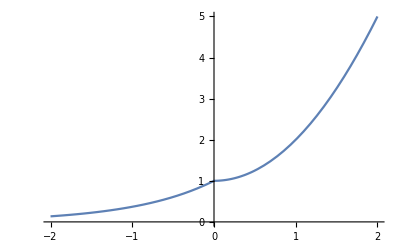

```mathematica
f[-3]
f[2]
Plot[f[x], {x, -2, 2}]
```

两个或多个变量的函数也可以用类似方式加以定义

```mathematica
f[x_,y_]:=x^2+Cos[y]
f[x_,x_]:=x+2x^2
f[2,3]
f[3,3]
f[u,v]+f[w,w]
```

4+Cos[3]

21

u^2+w+2 w^2+Cos[v]

例题：输入实数 a, b, c，输出平面 z = ax +by + c 在椭球 x^2/9+y^2/16+z^2/25=1 内的面积

```mathematica
f[a_,b_,c_]:=Sqrt[1+a^2+b^2]*NIntegrate[Boole[x^2/9+y^2/16+(a*x+b*y+c)^2/25≤1],{x,-5,5},{y,-4,4}];
```

```mathematica
f[1,2,3]
```

42.3572

### 8.1.2 立即赋值与延迟赋值

Mathematica 中有两种赋值形式： lhs =rhs 和 lhs := rhs， 其主要区别是什么时候计算; 的值.

lhs=rhs 是立即赋值， 即rhs是在赋值时立即计算，

lhs :=rhs 则是延时赋值， 即赋值时并不计算 rhs ， 而是在需要lhs的值时才进行计算.

1.例题：观察立即赋值和延迟赋值的调用结果

```mathematica
dex[x_]:=Expand[(1+x)^2]
ex[x_]=Expand[(1+x)^2]
ex[y+2]
dex[y+2]
```

1+2 x+x^2

1+2 (2+y)+(2+y)^2

9+6 y+y^2

例题：需要立即赋值的场合

General::ivar: 1+a is not a valid variable.

∂_(1+a) Log[Sin[1+a]]^2

2 Cot[x] Log[Sin[x]]

2 Cot[1+a] Log[Sin[1+a]]

General::ivar: 0.0000641782 is not a valid variable.

General::ivar: 0.0641783 is not a valid variable.

General::ivar: 0.128292 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

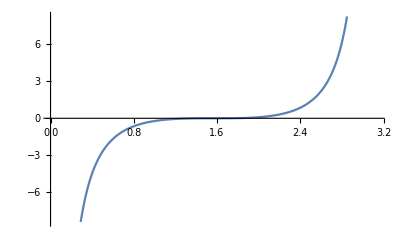

```mathematica
h[x_]:=D[Log[Sin[x]]^2,x]
h[1+a]
hd[x_]=D[Log[Sin[x]]^2,x]
hd[1+a]
Plot[h[x],{x,0,Pi}]
Plot[hd[x],{x,0,Pi}]
```

用:=定义的函数中， 调用时函数的值就会被反复计算.但在一些计算中，需要将同一组函数值使用多次， 这时就可以让 Mathematica 记住这些函数以节省时间.
f[x_]:=f[x]=rhs

例题：需要保存函数定义的情形

```mathematica
fb[1]=1;
fb[2]=1;
fb[n_]:=fb[n-1]+fb[n-2]
```

```mathematica
fb[20]//Timing
```

{0.015625,6765}

```mathematica
fb[n_]:=fb[n]= fb[n-1]+fb[n-2]
fb[30] // Timing
```

{0.,832040}

```mathematica
AbsoluteTiming[fb[30]]
```

{1.7×10^-6,832040}

使用过程如下： 当调用fb时,先计算fb[n-1]+ fb[n-2],再将结果保存到 fb[n], 运算时，使用能保存已有值的函数是一个好方法, 在
计算 f[30]时，需反复递推， 如需要反复计算 f[5]多次， 故此时记住 f[5]的值下次直接找出就比反复计算要好.在记住了一些函数值时， 査找就比计算快， 但这需要占用内存， 通常当重复计算的代价很大时保存函数值，且需要保存的函数不宜太多.

3.	= 和:= 不仅用来定义函数,还用来给变量赋值,x=value 立即求 value 的值,并将其赋于 x,而 x:=value 不立即求值， 每次使用 x 时才计算其值.

例题：观察变量延迟赋值的运算情况

```mathematica
a=1;
ir=a+2;
dr:=a+2
{ir,dr}
```

{3,3}

```mathematica
a=3;
{ir,dr}
```

{3,5}

可以用延时赋值 t := rhs 来设置在不同环境下有不同值的变量， 当每次需要t的值时， 就用与 rhs有关变量的当前值来计算它的值.

### 8.1.3 保存函数定义

Save[" file" ,symbol ] 将一个符号的完整定义存人一个文件

Save[" file.94, {object ,object2,.85 }]   保存一些对象的定义

例题 将函数f ，g, h 的定义写入temp 文件

```mathematica
f[x_]:=Sin[x];
Save["temp",f]
```

```mathematica
g[x_,y_]:=x+y
h[x_]:=Integrate[l/(l+x^2),x]
Save["temp", {g ,h}]
```

```mathematica
FilePrint["temp"]
```

f[x_] := Sin[x]
g[x_, y_] := x + y
 
h[x_] := Integrate[l/(l + x^2), x]
f[x_] := x^2 + 1 /; x >= 0
 
f[x_] := Exp[x] /; x < 0
 
f[x_] := Sin[x]
 
f[x_, x_] := x + 2*x^2
 
f[x_, y_] := x^2 + Cos[y]
 
f[a_, b_, c_] := Sqrt[1 + a^2 + b^2]*NIntegrate[
      Boole[x^2/9 + y^2/16 + (a*x + b*y + c)^2/25 <= 1], {x, -5, 5}, 
      {y, -4, 4}]
 
a = 3
g[x] = x^2
 
g[x_, y_] := x + y
 
h[x_] := Integrate[l/(l + x^2), x]

Save 将文件 temp 存在当前默认目录下，可用 Directory[] 査看 temp

在新打开的笔记本中可以调用保存的函数：

```mathematica
Directory[]
```

C:\Users\86189\Documents

```mathematica
<<temp
f[t]
g[a,b]
h[t]
```

Sin[t]

3+b

√l ArcTan[t/(√l)]

### 8.1.4 函数运算

1 .函数名是表达式

```mathematica
Clear[f,g]
```

```mathematica
f[x] + f[x^2] /. f -> g
InverseFunction[f][x]
ff[f_,x_]:=f[Sin[x]]+f[x+1]
ff[Exp,x]
```

g[x]+g[x^2]

f^(-1)[x]

ⅇ^(1+x)+ⅇ^Sin[x]

2.函数的重复调用

Nest[ f ,x ,n ]   f[x] 复合n次

NestList[f,x,n]   产生列表{s,f[x],f[f[x]],f[f[f[x]]],厎

Nest[f,x,4]

NestList[Cos, 1.0, 10]

FixedPoint[ f ,x ],    将f[x]迭代到结果不变为止

FixedPointList[f,x]   产生f[x]的迭代序列{x,f[x],f[f[x]],…瓆,直到结果不变为止

```mathematica
Clear[f]
```

```mathematica
f[x_]:=(x+3/x)/2
```

```mathematica
FixedPoint[f,0.6]
```

1.73205

```mathematica
NestList[f,1.0,10]
```

{1.,2.,1.75,1.73214,1.73205,1.73205,1.73205,1.73205,1.73205,1.73205,1.73205}

```mathematica
g[x_]:=Sqrt[2+x]
FixedPointList[g,1.5]
```

{1.5,1.87083,1.96744,1.99184,1.99796,1.99949,1.99987,1.99997,1.99999,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.,2.}

### 3.函数作用于列表和其他表达式

#### （1）Apply（替换节点，在第i层，注意i是从0开始取，层从0开始，树枝从1开始）

Apply[f,{a,b,...]                   f 作用于列表 f[a,b,.85]

f@@expr 或 Apply[f,expr]        用 f 作用于表达式的顶层.

Apply[f,expr,levelspec]           f 作用于表达式的指定层.

Apply[f]                      表示 Apply的运算符形式，它可以应用于表达式.

```mathematica
Exp[{x,y,z}]
```

{ⅇ^x,ⅇ^y,ⅇ^z}

```mathematica
Apply[f,{x,y,z}]
f@@{x, y, z}
```

f[x,y,z]

f[x,y,z]

```mathematica
f@@{{a, b, c}, {x, y, z}}
```

f[{3,b,c},{x,y,z}]

```mathematica
Apply[f, <|1 -> a, 2 -> b, 3 -> {c},4->6|>]
```

f[3,b,{c},6]

可以指定f 作用于列表的不同层

```mathematica
Apply[f,{{a,b,c},{d,e}},{1}]
```

{f[3,b,c],f[d,e]}

```mathematica
Apply[f,{{a,b,c},{d,e}},{0,1}]
```

f[f[3,b,c],f[d,e]]

```mathematica
Clear[f];
Clear[a];
Apply[f,{a}]
Apply[f,{{{a}}},{0}]
Apply[f,{{{a}}},{1}]
Apply[f,{{{a}}},{2}]
```

f[a]

f[{{a}}]

{f[{a}]}

{{f[a]}}

```mathematica
Apply[f,{{{{{a}}}}},{0,2}]
Apply[f,{{{{{a}}}}},{0,1}]
```

f[f[f[{{a}}]]]

f[f[{{{a}}}]]

```mathematica
Apply[f,{{{{{a}}}}},{0,Infinity}]
```

f[f[f[f[f[a]]]]]

#### （2）Map

当有一系列元素时，经常需要将一个函数分别作用于每一项中，这可以用Map来实现。

Map[f,expr] 或 f/@expr      将 f 应用到 expr 中第一层的每个元素.

Map[f,expr,level]           将 f 应用到 level 指定的 expr 的部分中.
f 作用到 expr 的第 1 层到第 n 层   level=n
f 只对 expr 的第 n 层作用 level={n}

TreeForm[expr]          按树的层次形式输岀表达式

```mathematica
Map[f,{a,b,c}]
```

{f[a],f[b],f[c]}

```mathematica
f/@ {a, b, c }
```

{f[a],f[b],f[c]}

```mathematica
Map[Sqrt,g[x^2,x^3]]
```

g[√(x^2),√(x^3)]

```mathematica
Map[f, a + b+ c]
```

f[a]+f[b]+f[c]

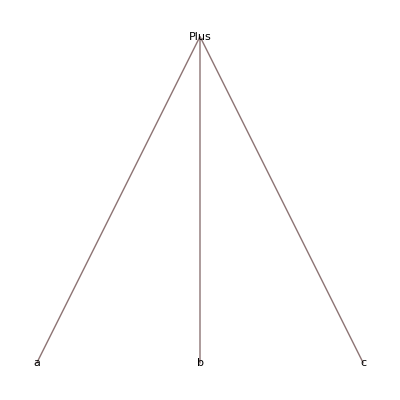

```mathematica
TreeForm[a + b + c]
```

```mathematica
Function[x, x^2] /@ {1, 2, 3, 4}
```

{1,4,9,16}

```mathematica
Map[f, {{a, b}, {c, d, e}}, {2}] (*作用到第2层*)
```

{{f[a],f[b]},{f[c],f[d],f[e]}}

```mathematica
Map[f, {{a, b}, {c, d, e}}, 2]  (*作用到第1-2层*)
```

{f[{f[a],f[b]}],f[{f[c],f[d],f[e]}]}

```mathematica
Map[f, {{{{{a}}}}}, 3]
```

{f[{f[{f[{{a}}]}]}]}

不论表达式的 head 为何种形式，都可使用 Map

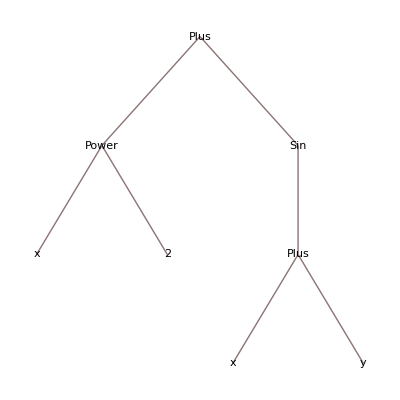

```mathematica
TreeForm[x^2 + Sin[x+y]]
```

```mathematica
Map[f, x^2 +Sin[x+y], 2]
```

f[f[x]^f[2]]+f[Sin[f[x+y]]]

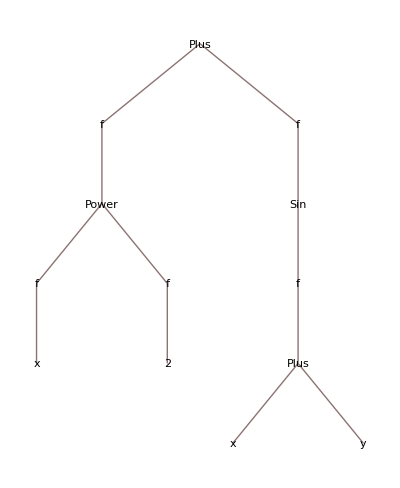

```mathematica
TreeForm[%]
```

#### (3)MapAll

MapAll[f,expr]或 f//@expr        将 f 作用到 expr 的每个子表达式上.

```mathematica
f//@{{a, b}, {c}, {{d}}}
```

f[{f[{f[a],f[b]}],f[{f[c]}],f[{f[{f[d]}]}]}]

```mathematica
MapAll[f, x^2 + y^2]
```

f[f[f[x]^f[2]]+f[f[y]^f[2]]]

```mathematica
temp=a+b^y^z;
{Map[Sin,temp,{2}], Map[Sin,temp,{3}]}
{Map[Sin,temp,2], Map[Sin,temp,3]}
```

{a+Sin[b]^Sin[y^z],a+b^(Sin[y]^Sin[z])}

{Sin[a]+Sin[Sin[b]^Sin[y^z]],Sin[a]+Sin[Sin[b]^Sin[Sin[y]^Sin[z]]]}

#### (4)MapAt（增加节点（在第n个树枝上增加节点，树枝从1开始计数））

MapAt[f,expr,n] f作用于expr中位置n上的元素. 如果n为负数,从末尾开始计数.

MapAt[f,expr,{i,j,...]  将 f 作用于 expr 中位置 {i,j,厎 上的元素.

MapAt[f,expr,{{i1,j1,...},{i2,j2,...},...] 将 f 作用于expr中指定的几个位置上的元素.

```mathematica
MapAt[f, {a, b, c, d,e }, 2]
```

{a,f[b],c,d,e}

```mathematica
MapAt[f, {a, b, c, d,e}, {{1}, {4},{5}}]
```

{f[a],b,c,f[d],f[e]}

```mathematica
MapAt[f, {{a, b, c}, {d, e}}, {1,2}]
```

{{a,f[b],c},{d,e}}

```mathematica
MapAt[f, {{a, b, c}, {d, e}}, {All, 2}]
```

{{a,f[b],c},{d,f[e]}}

```mathematica
MapAt[f, a + b + c + d, 2]
```

a+c+d+f[b]

```mathematica
MapAt[f, x^2 + y^2, {{1, 1}, {2, 2}}]
```

y^f[2]+f[x]^2

## §8.2 模式替换

### 1.模式

Mathematica 中用大量的模式来代表各类表达式， Mathematica 模式的标志是￿￿，其基本规则是代表任意表达式.例如 f[x_ ]表示形如f[ anything ]的表达式，并且将表达式 angthing 命名为 x 以便在变换规则中引用. 可以将.94_.94放到表达式的任何位置， 得到与能以任何方式填充的表达式匹配的模式。由于 Mathematica 中的许多运算可用于一类表达式，所以模式就十分有效。
模式的主要功能在于 Wolfram 语言中的许多操作不仅可以对单个表达式实现，也可以对代表某类表达式的模式进行操作.

(1)用模式给出一类表达式的变换规则：

```mathematica
f[a] + f[b] /. f[x_] -> x^2
```

a^2+b^2

(2)用模式在指定类中找出表达式的位置：

```mathematica
Position[{f[a], g[b], f[c]}, f[x_]]
```

{{1},{3}}

(3)只有与模式匹配的表达式会执行操作

```mathematica
f[{a, b}] + f[a*b] /. f[{x_, y_}] -> p[x + y]
```

f[a b]+p[a+b]

例题：
           f[n_]                     变量名为 n 的 f
           f[n_,m_]               变量名为 n 和 m 的 f
           x^n_                     指数为 n 的 x 的幂
           x_^n_                   任何次幂的表达式
           a_+b_                   两个表达式的和
          {a1_,a2_}             两个表达式组成的列表
          f[n_,n_]               有两个相同 变量的 f

Wolfram 语言的模式代表一类给定结构 的表达式. 当一个表达式的结构与模式的结构相同时，这个表达式就可以用在模式中. 如果数学上完全相同的两个表达式，当它们的结构不同时，也不能用同一个模式来表示.

### 2.模式命名

对象如 x_ 表示任何表达式，并将此表达式命名为 x. 
一个要点是，当使用 x_ 时，Wolfram 语言要求在特定表达式中具有 x 名的表达式是相同的.因此，f[x_,x_] 表示 f 的两个变量完全相同. 而 f[_,_] 可以表示形如 f[x,y] 的表达式，其中该表达式中的变量 x 和 y 不必相同.

```mathematica
{f[a, a], f[a, b]} /. f[x_, x_] -> p[x]
```

{p[a],f[a,b]}

在 Wolfram 语言中，不仅可以对一个空位命名，而且可以对模式中的任何部分命名，

x:pattern 表示命名为 x 的模式.

在变换规则中，可以将这种机制用到模式的任何部分以便在变换规则的右端使用.
_	            任何表达式
x_              命名为 x 的任何表达式
x:pattern	     与 pattern 匹配的名为 x 的表达式

```mathematica
f[a^b] /. f[x : _^n_] -> p[x, n]
```

p[a^b,b]

```mathematica
{f[g[3], g[3]], f[g[4], g[2]]} /. f[x : g[_], y_] -> r[x]  (*_ 命名为x， *)
{f[g[3], g[3]], f[g[4], g[2]]} /. f[x : g[_], x_] -> r[x]
```

{r[g[3]],r[g[4]]}

{r[g[3]],f[g[4],g[2]]}

### 3.寻找与模式匹配的表达式

Cases[list,form]                   给出与 form 匹配的 list 中的元素

Count[list,form]	    给出与 form 匹配的 list 中元素的个数

Position[list,form,{1}]	    给出与 form 匹配的 list 中的元素的位置

Select[list,test]                     给出使 test 的值为 True 的 list 中的元素

Pick[list,sel,form]	    给出使 sel 的相应元素与 form 匹配的 list 中的元素

```mathematica
Cases[{(1 + a)^2,   1 + 2 a + a^2, (1 + Sin[b])^2, (1 + x^3)^2, (1 + x + y)^2}, (1 + x_)^2]
Count[{3, 4, x, x^2, x^3}, x^_]
```

{(1+a)^2,(1+Sin[b])^2,(1+x^3)^2,(1+x+y)^2}

2

像 Cases 这样的函数不仅可以用于列表，而且可以用于任何表达式，可以指定项所在的层.

Cases[expr,lhs->rhs]	    在 expr 中寻找与 lhs 匹配的元素，并对其进行变换

Cases[expr,lhs->rhs,lev]    测试指定层 lev 上表达式 expr 的项

Count[expr,form,lev]	    给出指定层 lev 上与模式 form 匹配的项数

Position[expr,form,lev]	    给出指定层 lev 上与模式 form 匹配的项的位置

```mathematica
Position[{4, 4+x^a, x^b, 6+x^5}, x^_, All, 2]
```

{{2,2},{3}}

```mathematica
Cases[{3, 4, x, x^2, x^3}, x^n_ -> n]
```

{2,3}

DeleteCases[expr,form]	     删除表达式 expr 中与 form 匹配的元素

DeleteCases[expr,form,lev]	 删除表达式 expr 的指定层 lev 中与 form 匹配的项

```mathematica
DeleteCases[{3, 4, x, x^2, x^3}, x^n_]
```

{3,4,x}

```mathematica
DeleteCases[{3, 4, x, 2 + x^2, 3 + 5x}, _Integer, All]
```

{x,x,x}

```mathematica
DeleteCases[{3, 4, x, 2 + x^2, 3 + 5 x}, _Integer, {2}]
```

{3,4,x,x^2,5 x}

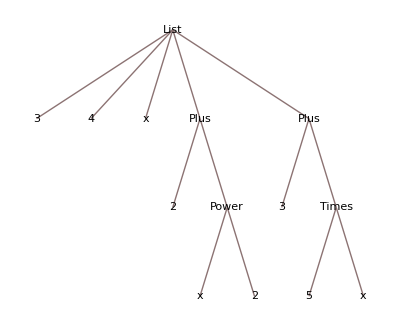

```mathematica
TreeForm[{3,4,x,2+x^2,3+5 x}]
```

### 4.模式替换

lhs->rhs 或 lhs→rhs     表示将 lhs 转换为 rhs 的规则.

规则是一种通用的结构，可以表示表达式之间的转换、子代、对应关系和其他关系, 
可以用 Replace 等指令来应用规则,
 lhs = rhs 赋值指定无论何时都应使用规则 lhs -> rhs

以模式名称出现在 lhs 中的符号被看作规则中的局部符号.当符号出现在 lhs 中 /; 条件的右边以及 lhs 中任意位置上，甚至其它的范围结构内时，这都是成立的.

```mathematica
Sin[x] /. Sin -> Arctan
```

Arctan[x]

```mathematica
x /. {x -> 1, x -> 3, x -> 7}  (*应用第一个规则*)
```

1

```mathematica
x /. {{x -> 1}, {x -> 3}, {x -> 7}} (* 分别应用每个规则 *)
```

{1,3,7}

```mathematica
l + x^(1/2) + x^2 /. x^n_ -> g[m]  (*用模式把变量和匹配的部分结合在一起*)
```

l+2 g[m]

```mathematica
Sin[2x]+Sin[2y z]+Sin[z]/. Sin[2x_]->2Sin[x]Cos[x]
```

2 Cos[x] Sin[x]+Sin[z]+2 Cos[y z] Sin[y z]

```mathematica
x /. {y -> 2, z -> 3}(*如果没有相匹配的规则，则返回原来的表达式*)
```

x

为模式替换取名并保存到变量中， 调用更方便。

```mathematica
s=Sin[x_]->2 Sin[x/2] Cos[x/2]
```

Sin[x_]→2 Cos[x/2] Sin[x/2]

```mathematica
Sin[2x]+Sin[2y z]+Sin[z]/.s
```

2 Cos[x] Sin[x]+2 Cos[z/2] Sin[z/2]+2 Cos[y z] Sin[y z]

### 5. 立即变换和延迟变换

lhs->rhs  在定义规则时rhs被求值

lhs:>rhs 或 lhs  :>rhs  在定义规则时 rhs 不求值， 调用规则时才求值
（字符 :> 可以输入为 :> 或 ∖[RuleDelayed].）

```mathematica
x:>RandomReal[]
```

x:>RandomReal[]

```mathematica
{x,x,x}/.x:>RandomReal[]
```

{0.316564,0.857046,0.7846}

```mathematica
n=1;{x,x,a,b,x,x,c,d}/.x:>n++
```

{1,2,a,b,3,4,c,d}

```mathematica
f[x]->Expand[(1+x)^2]
g[x_]:>Expand[(1+x)^2]
```

f[x]→1+2 x+x^2

g[x_]:>Expand[(1+x)^2]

```mathematica
f[a+b]/.f[x_]->Expand[(1+x)^2]
g[a+b]/.g[x_]:>Expand[(1+x)^2]
```

1+2 (a+b)+(a+b)^2

1+2 a+a^2+2 b+2 a b+b^2

### 6. 调用规则

将模式替换应用到具体的函数定义或其他表达式中需要调用替换规则，一般有以下调用方式.

Replace[expr,rules]应用一个规则或规则列表来转换整个表达式 expr

Replace[expr,rules,level]应用规则到 expr 中由 level指定的部分

ReplaceAll[expr,rules]
Expr/.rules应用一个规则或规则列表尽可能转换一个表达式 expr 的每个子部分

ReplaceRepeated[expr,rules]
expr//.rules重复执行替换直至 expr 不再改变.

ReplaceList[expr,rules]
以所有可能的方式应用一个规则或规则列表转换整个表达式 expr，并返回取得的结果列表.

```mathematica
{x,x^2,y,z}/.x->{a,b}
```

{{a,b},{a^2,b^2},y,z}

```mathematica
ReplaceAll[{x,x^2,y,z},x->{a,b}]
```

{{a,b},{a^2,b^2},y,z}

例题：比较两种调用 /.   //.

```mathematica
rules={Log[x_ y_]:>Log[x]+Log[y],Log[x_^k_]:>k Log[x]};
```

```mathematica
Log[Sqrt[a (b c^d)^e]]/.rules
```

1/2 Log[a (b c^d)^e]

```mathematica
Log[Sqrt[a (b c^d)^e]]//.rules
```

1/2 (Log[a]+e (Log[b]+d Log[c]))

```mathematica
{f[f[x]], f[x], g[f[x]], f[g[f[x]]]} //. f[x_] -> x
```

{x,x,g[x],g[x]}

```mathematica
{f[f[x]], f[x], g[f[x]], f[g[f[x]]]}/. f[x_] -> x
```

{f[x],x,g[x],g[f[x]]}

使用 //. 算符时，应该非常小心以避免出现无限循环. 例如，命令 x//.x->x+1 就将导致一个无限循环

调用规则前是否进行计算

```mathematica
Hold[{f[f[x]], f[x], g[f[x]], f[g[f[x]]]} ] //. f[x_] :> x + x
Hold[{f[f[x]], f[x], g[f[x]], f[g[f[x]]]} ] //. f[x_] -> x + x
```

Hold[{(x+x)+(x+x),x+x,g[x+x],g[x+x]+g[x+x]}]

Hold[{2 (2 x),2 x,g[2 x],2 g[2 x]}]

```mathematica
ReplaceList[a + b + c, x_ + y_ -> g[x, y]]
```

{g[a,b+c],g[b,a+c],g[c,a+b],g[a+b,c],g[a+c,b],g[b+c,a]}

## §8.3 给模式附加条件

### 1. 模式中的表达式类型限制

可以通过头部来区分不同￿类型￿的表达式，如整数的头部为 Integer，而列表的头部为 List.

x_h	          具有头部 h 的表达式

x_Integer       整数型

x_Real	          实数型

x_Complex    复数型

x_List	          列表型

x_Symbol      符号型

```mathematica
{a, 4, 5, Exp[2]} /. x_Integer -> p[x]
```

{a,p[4],p[5],ⅇ^p[2]}

```mathematica
d[x_^n_Integer]:=n x^(n-1)
```

```mathematica
d[x^4]+d[(a+b)^3]+d[x^(2.0)]
```

3 (a+b)^2+4 x^3+d[x^2.]

### 2. Mathematica中提供了对模式进行限制的一般方法.

pattern/;condition	    当条件满足时，模式才匹配

lhs:>rhs/;condition	    当条件满足时，才使用规则

lhs:=rhs/;condition	    当条件满足时，才使用定义

在 Wolfram 语言中有一类函数去测试表达式的性质. 这类函数后有一个 Q，表明它们在.93提问.94.

IntegerQ[expr]整数      EvenQ[expr]偶数

OddQ[expr]奇数          PrimeQ[expr]素数

NumberQ[expr]任何数     NumericQ[expr]数字型

PolynomialQ[expr,{x1,x2,.85}]关于 x1, x2, .85 的多项式

VectorQ[expr]表示向量的列表

MatrixQ[expr]表示矩阵的集合的列表

VectorQ[expr,NumericQ],  MatrixQ[expr,NumericQ]
所有元素都是数字的向量和矩阵VectorQ[expr,test]

MatrixQ[expr,test]对所有元素 test 的函数值都为 True 的向量和矩阵

ArrayQ[expr,d]深度与 d 匹配的完全数组

```mathematica
{2.3, 4, 7/8, a, b}/.(x_/;NumberQ[x])->x^2
```

{5.29,16,49/64,a,b}

```mathematica
mi[list_] := list^2 /; VectorQ[list, IntegerQ]
```

```mathematica
{mi[{2, 3}], mi[{2.1, 2.2}], mi[{a, b}]}
```

{{4,9},mi[{2.1,2.2}],mi[{a,b}]}

```mathematica
{6, -7, 3, 2, -1, -2} /. x_ /; x < 0 -> w
```

{6,w,3,2,w,w}

pattern/;condition 通过所涉及模式名满足的条件确定是否可以匹配.

pattern?test 通过检查函数 test 在表达式的值来确定是否可以匹配.

用 ? 比 /; 更方便.
运算符 ? 有一个高的优先级. 这样 _^_?t 是 _^(_?t)，而不是 (_^_)?t

```mathematica
p[x_?NumberQ] :=Sin[x^2]
```

```mathematica
p[4.5] + p[3/2] + p[u]
```

1.7636+p[u]

```mathematica
Cases[{1, 2, 3.5, x, y, 4}, _?NumberQ]
```

{1,2,3.5,4}

```mathematica
MatchQ[{1, E, Pi}, {__?Positive}]
```

True

Except[c]与任何非 c 表达式匹配的模式

Except[c,patt]与 patt 匹配但非 c 的模式

patt1|patt2|￿      多种形式的模式

```mathematica
Cases[{a, Sin[1], 0, 1, 2, x^2},Except[_Integer]]
```

{a,Sin[1],x^2}

```mathematica
{1, x, x^2, x^3, a^x} /. (x | x^_) -> q
```

{1,q,q,q,a^q}

```mathematica
h[a | b] := Sin[a]
```

```mathematica
Clear[f,g]
```

```mathematica
{h[a], h[b], h[x]}
```

{Sin[a],Sin[a],h[x]}

## §8.4. 参数数目可变函数

1.	模式 f[x_,y_] 仅代表恰有两个变量的函数. 有时还需要建立具有任意数目的自变量的函数.这可以通过多重空位来实现. 一个空位 x_ 表示一个 Wolfram 语言表达式，两个空位 x__ 表示多个表达式.

_单一表达式
x_名为 x 的表达式
__一个或多个表达式序列
x__名为 x 的表达式列
x__h头部为 h 的表达式列
___零个或多个表达式序列
x___名为 x 的零个或多个表达式序列
x___h头部为 h 的零个或多个表达式序列

例题：定少用多

```mathematica
f[x__]:=p[x,x,x]
f[a,b,c]
```

p[a,b,c,a,b,c,a,b,c]

```mathematica
g[x__]:=x+x*x
g[a,b,c,d]
```

a+b+c+d+a^2 b^2 c^2 d^2

```mathematica
h[a___,x_,b___,x_,c___]:=hh[x]*h[a,b,c]
h[2,3,2,5,3,1]
```

h[5,1] hh[2] hh[3]

2.	可选变量与默认变量
有时需要定义具有默认值的函数. 即省略某些变量时，其值就用设定的默认值代替. 模式 x_:v 就表示省略时值为 v 表示的变量.

x_:v	   省略时值用 v 代替的表达式

x_h:v	   具有头部 h 和默认值 v 的表达式

x_.	   具有设定默认值的表达式

```mathematica
j[x_,y_:1,z_:2]:=E^(-x)(y^2+z^2)
j[3]
```

5/ⅇ^3

一些 Wolfram 语言常用函数的变量具有系统设定的默认值，此时不能明确给出 x_:v 中的默认值，而是可用 x_. 来使用其系统设定的默认值.
x_+y_.	  y 的默认值为 0
x_y_.	      y 的默认值为 1
x_^y_.	  y 的默认值为 1

利用 x_. 可以使一个模式与几个不同的表达式匹配，当需要与多个结构不同但数学形式相同的表达式匹配时这种方式特别方便.

```mathematica
{f[a], f[a + b]} /. f[x_ + y_.] -> p[x, y]
```

{p[a,0],p[b,a]}

```mathematica
Clear["Global`*"]
{g[a^2], g[a + b]} /. g[x_^n_] -> p[x, n]
```

{p[a,2],g[a+b]}

```mathematica
{g[a^2], g[a + b]} /. g[x_^n_.] -> p[x, n]
```

{p[a,2],p[a+b,1]}

```mathematica
lin[a_. + b_. x_, x_] := p[a, b]
```

```mathematica
lin[1 +5 x, x]
```

p[1,5]

## §8.5 函数的属性与属性定义

1.	在 Mathematica 中不仅可以定义函数的运算规则， 还可以设置函数的属性。
函数的属性对函数的运算规则和调用时对模式匹配有直接的作用和影响

Attributes[f]	           列出赋予 f 的属性

SetAttributes[f,attr]	   给 f 赋予属性 attr

ClearAttributes[f,attr]	   清除 f 的属性 attr

```mathematica
Attributes[Plus]
Attributes[Sqrt]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

{Listable,NumericFunction,Protected}

一个符号 f 的可能属性的完整列表是：

Constant        f的所有导数为0

Flat          	f 是可结合的 f[f[a,b],c]与f[a,b,c]等价

HoldAll	        f 的所有参数都不参与运算

HoldAllComplete	f 的参数完全与运算隔离

HoldFirst     	f 的第一个参数不参与运算

HoldRest     	除第一个参数外的 f 的其它参数不参与运算

Listable	  f 自动线性作用于整个列表

Locked	        f 的属性不能被更改

NHoldAll     	f 的参数不受N 的影响

NHoldFirst	    f 的第一个参数不受 N 的影响

NHoldRest	    除第一个参数外的 f 的其它参数不受 N 的影响

NumericFunction	参数是数时，f 的值也假定为一个数

OneIdentity	    f[a]、f[f[a]]等在模型匹配中与 a 等价

Orderless	    f 可交换

Protected	    f 的值不能被更改

ReadProtected	f 的值不能被读出

SequenceHold	f 的参数中的 Sequence 对象不被展平

```mathematica
SetAttributes[q, Orderless]
```

```mathematica
q[b,a,c]
f[q[a, b], q[b, c]] /. f[q[x_, y_], q[x_, z_]] -> p[x, y, z]
```

q[a,b,c]

p[b,a,c]

Wolfram 语言在进行匹配时，也考虑到了可结合性，如模式 g[x_+y_] 可以和 g[a+b+c] 匹配，此时 x→a 并且 y→(b+c).

```mathematica
g[a+b+c]/.g[x_+y_]->p(x,y)
```

如果没有其他限制时，Wolfram 语言把 x_ 与和式中的第一个元素匹配：

```mathematica
g[a+b+c+d]/.g[x_+y_]->p(x,y)
Replacelist[g[a+b+c],g[x_,y_]->p(x,y)]
```

例题：满足结合律的函数

```mathematica
SetAttributes[h,Flat]
```

```mathematica
h[a,b,a,b]/.h[x_,x_]->rp[x]
```

rp[h[a,b]]

```mathematica
h[a,b,b,c]/.h[x_,x_]->rp[x]
```

h[a,rp[h[b]],c]

如果要增加某函数的性能，那么先要去掉保护属性。作出变换规则或定义后，再恢复内部函数的保护属性.

```mathematica
Log[a b c]
```

Log[a b c]

```mathematica
Unprotect[Log]
Log[x_ y_]:=Log[x]+Log[y]
Log[x_^n_]:=n Log[x]
Protect[Log]
```

{Log}

{Log}

```mathematica
Log[a b c]
```

Log[a]+Log[b]+Log[c]

```mathematica
Log[a^2 b^2 c^(1/3)]
```

2 Log[a]+2 Log[b]+Log[c]/3

例题：定义简单的积分函数

```mathematica
int[y_+z_,x_]:=int[y,x]+int[z,x];int[c_ y_,x_]:=c int[y,x]/;FreeQ[c,x]
```

```mathematica
int[c_,x_]:=c x/;FreeQ[c,x]
int[x_^n_.,x_]:=x^(n+1)/(n+1)/;FreeQ[n,x]&&n≠-1
int[1/(a_.x_+b_.),x_]:=Log[a x+b]/a/;FreeQ[{a,b},x]
int[Exp[a_.x_+b_.],x_]:=Exp[a x+b]/a/;FreeQ[{a,b},x]
```

```mathematica
int[a x+b x^2+3,x]
```

3 x+(a x^2)/2+(b x^3)/3

```mathematica
int[a x+b x^2+3,x]
```

3 x+(a x^2)/2+(b x^3)/3

```mathematica
int[1/(2 p x-1),x]
```

Log[-1+2 p x]/(2 p)

Wolfram 系统一旦运算了表达式的头部，就会查看该头部是否是具有属性的符号.
   如果符号具有 Orderless、Flat 或 Listable属性，则 Wolfram 系统在运算表达式的元素之后，将立即执行与这些属性关联的转换.

标准运算过程的下一步是将 Wolfram 系统所知道的定义用于正在运算的表达式.
   Wolfram 系统首先尝试使用您创建的定义，如果没有适用的定义，再尝试使用内置定义.
   如果 Wolfram 系统找到适用的定义，它将对表达式执行相应的转换.结果是另一个表达式.

#### 标准运算过程.

■ 运算表达式的头部.■ 依次运算每个元素.■ 应用与属性 Orderless、Listable 和 Flat 关联的转换.■ 应用您给出的定义.■ 应用内置定义.■ 运算结果.

2. 在运算过程中可以用.93Trace[expr] .94跟踪 Mathematica 计算 expr 的工作过
程。下列为计算表达式的跟踪形式：

Trace[expr] 产生计算 expr 过程中的所有表达式的一个列表.

Trace[expr, form] 仅包括匹配 form 的表达式.

Trace[expr, s] 包括所有使用和符号 s 相关联的变换规则的计算.

```mathematica
a=7;
Trace[2 a x+a^2+x^2]
```

{{{a,7},2 7 x,14 x},{{a,7},7^2,49},14 x+49+x^2,49+14 x+x^2}

2 ax + a^2 + x^2 内部形式  为 Plus[Times[2, a, x], Power[a, 2], Power[x^2]]

## §8 .6 纯函数

body & 或 Function[body] 是一个纯 （或￿匿名￿） 函数.形式参数是 # （或 #1）、#2等.

Function[x, body] 具有一个形式参数的纯函数

Function[{x1, x2, ...}, body]具有多个形式参数的纯函数.

Function[params, body, attrs] 是一个纯函数，在计算时被认为具有属性 attrs.

说明：

（1） 当 Function[body] 或 body & 用到参数集合上时，# （或 #1） 由第一个参数代替，#2 由第二个代替，以此类推.#0 由函数本身代替.

（2） 如果给出的参数比函数中 # i 数目更多的话，剩余的参数被忽略.

（3） ## 表示提供的所有参数的序列.## n 表示从数字 n 开始的参数.

（4） Function 有属性 HoldAll.仅在形式参数被自变量替换后计算函数体.

（5） Function 结构可以以任意方式嵌套.每种方式都可以当作作用域结构处理

（6） 在 Function[params, body, attrs] 中，attrs 可以是一个属性或属性列表.例题：纯函数定义

(1) 1 个参数

```mathematica
Function[u,Cos[u]+u Sin[u]][x]
```

Cos[x]+x Sin[x]

```mathematica
Function[Cos[#]+# Sin[#]][x]
```

Cos[x]+x Sin[x]

```mathematica
(Cos[#]+# Sin[#])&[x]
```

Cos[x]+x Sin[x]

（2） 两个参数

```mathematica
Function[{u,v},u Cos[v]+Log[u+v]][x,y]
```

x Cos[y]+Log[x+y]

```mathematica
(# Cos[#2]+Log[#+#2])&[x,y]
```

x Cos[y]+Log[x+y]

```mathematica
f=(# Cos[#2]+Log[#+#2])&
f[3,2]
```

#1 Cos[#2]+Log[#1+#2]&

3 Cos[2]+Log[5]

(3) 将纯函数映射到列表

```mathematica
{#,#^2}&/@{x,y,z}
```

{{x,x^2},{y,y^2},{z,z^2}}

(4) 从纯函数中创建一个矩阵

```mathematica
MatrixForm[Array[(#+#2^2&),{3,4}]]
```

(2 | 5 | 10 | 17
3 | 6 | 11 | 18
4 | 7 | 12 | 19)

(5) 按数组的第二个元素排序

```mathematica
Sort[{{a,2},{c,1},{d,3}},#1[[2]]<#2[[2]]&]
```

{{c,1},{7,2},{d,3}}

(6) 函数名直接运算

```mathematica
Sec'
```

Sec[#1] Tan[#1]&

(7) ## 表示所有参数

```mathematica
Clear["Global`*"]
f[X,##,Y,##]&[a,b,c]
```

f[X,a,b,c,Y,a,b,c]

```mathematica
g[X,##2,Y,##3,Z,##4]&[a,b,c,d]
```

g[X,b,c,d,Y,c,d,Z,d]

(8) 创建一个具有 Listable 属性的纯函数

```mathematica
Function[{u},g[u],Listable][{a,b,c}]
```

{g[a],g[b],g[c]}

```mathematica
Function[{u},g[u]][{a,b,c}]
```

g[{a,b,c}]